# Cryptocurrencies explorations

## Introduction

The main goal of this computational Markdown document is to provide some basic views and insights into the landscape of cryptocurrencies. The “landscape” we consider consists of price action and trading volume time series for cryptocurrencies found in Yahoo Finance.

In this document we compute and plot with Raku the statistics in [AA1].

### Details on "running" the document

The Raku package used for data retrieval is "Data::Cryptocurrencies", [AAp1]. The JavaScript D3 plots are made via "JavaScript::D3", [AAp2].

This Markdown document is converted to its woven Markdown version with "Text::CodeProcessing", [AAp3]. The woven Markdown document is converted to an HTML document with "Markdown::Grammar", [AAp4].

Here is the corresponding shell command:

file-code-chunks-eval Cryptocurrencies-explorations.md &&    
  from-markdown Cryptocurrencies-explorations_woven.md -t html -o Cryptocurrencies-explorations.html &&
  open Cryptocurrencies-explorations.html

## Setup

Here we load the packages used below:

use Data::Cryptocurrencies;
use Data::Reshapers;
use Data::Summarizers;
use Text::Plot;
use JavaScript::D3;
use Mathematica::Serializer;

(Any)

## Time series

Here we get Bitcoin (BTC) data from 1/1/2020 until now:

my %ccTS = cryptocurrency-data(<BTC ETH>, dates => (DateTime.new(2020,1,1,0,0,0), now), props => <DateTime Close>, format => 'hash'):cache-all;

say %ccTS.elems;

2

Here is a summary:

records-summary(%ccTS);

summary of ETH =>
+--------------------------------+--------------------------+
| DateTime                       | Close                    |
+--------------------------------+--------------------------+
| Min    => 2020-01-01T00:00:37Z | Min    => 110.605873     |
| 1st-Qu => 2020-10-16T12:00:37Z | 1st-Qu => 401.866287     |
| Mean   => 2021-08-03T00:00:37Z | Mean   => 1681.823401621 |
| Median => 2021-08-03T00:00:37Z | Median => 1562.740112    |
| 3rd-Qu => 2022-05-20T12:00:37Z | 3rd-Qu => 2614.046387    |
| Max    => 2023-03-06T00:00:37Z | Max    => 4812.087402    |
+--------------------------------+--------------------------+
summary of BTC =>
+---------------------------+--------------------------------+
| Close                     | DateTime                       |
+---------------------------+--------------------------------+
| Min    => 4970.788086     | Min    => 2020-01-01T00:00:37Z |
| 1st-Qu => 11904.569336    | 1st-Qu => 2020-10-16T12:00:37Z |
| Mean   => 28503.208946593 | Mean   => 2021-08-03T00:00:37Z |
| Median => 23164.628906    | Median => 2021-08-03T00:00:37Z |
| 3rd-Qu => 42247.5097655   | 3rd-Qu => 2022-05-20T12:00:37Z |
| Max    => 67566.828125    | Max    => 2023-03-06T00:00:37Z |
+---------------------------+--------------------------------+

Here are D3.js plots:

my %ts4 = %ccTS.map({ $_.key => $_.value.map(-> %r { %( date => %r<DateTime>.Str.substr(0,10), value => %r<Close>.Numeric, group => $_.key ) }).grep({ $_.<value> ~~ Numeric }) });
say %ts4>>.elems;

{BTC => 1161, ETH => 1161}

deduce-type(%ts4<BTC>)

Vector(Struct([date, group, value], [Str, Str, Rat]), 1161)

js-d3-date-list-plot(%ts4<BTC>, plot-label => 'BTC', width => 800, height => 400, format => 'html', div-id => 'BTC');

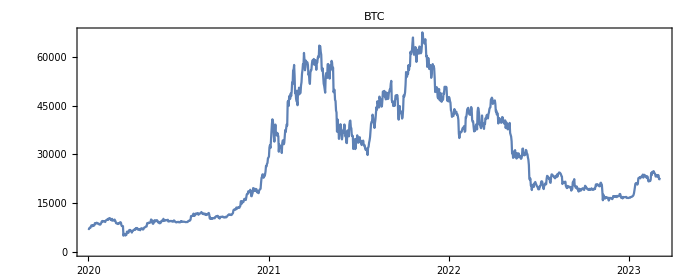

```mathematica
DateListPlot[RakuInputExecute["%ts4<BTC> ==> encode-to-wl"][List,{#date,#value}&],ImageSize->700,PlotLabel->"BTC",PlotTheme->"Detailed",AspectRatio->1/2.5]
```

js-d3-date-list-plot(%ts4<ETH>, plot-label => 'ETH', width => 800, height => 400, format => 'html', div-id => 'ETH');

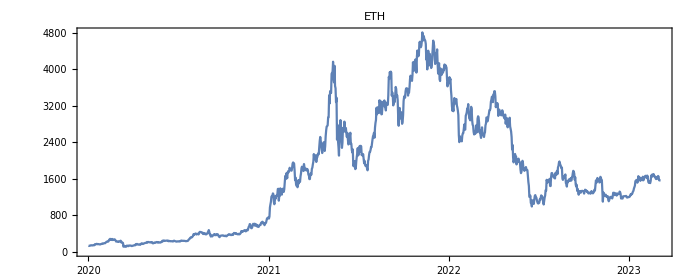

```mathematica
DateListPlot[RakuInputExecute["%ts4<ETH> ==> encode-to-wl"][List,{#date,#value}&],ImageSize->700,PlotLabel->"ETH",PlotTheme->"Detailed",AspectRatio->1/2.5]
```

## Pareto principle adherence

Get data for all cryptocurrencies:

my @dsData = cryptocurrency-data('all', dates => (now - 14 * 24 * 3600, now), props => <Symbol DateTime Close Volume>, format => 'dataset');
say "Dimensions : {dimensions(@dsData)}.";

Dimensions : 307 4.

Clean data and show summary:

@dsData = @dsData.grep({ $_<Close> ~~ Numeric });
records-summary(@dsData);

+----------------+---------------------------+-----------------------------+--------------------------------+
| Symbol         | Close                     | Volume                      | DateTime                       |
+----------------+---------------------------+-----------------------------+--------------------------------+
| XMR     => 14  | Min    => 0.023923        | Min    => 10200068          | Min    => 2023-02-21T00:00:37Z |
| USDC    => 14  | 1st-Qu => 0.342737        | 1st-Qu => 115814399         | 1st-Qu => 2023-02-24T00:00:37Z |
| BCH     => 14  | Mean   => 1219.5061651054 | Mean   => 3234118071.027211 | Mean   => 2023-02-27T12:00:37Z |
| ETC     => 14  | Median => 1.194818        | Median => 288398306.5       | Median => 2023-02-27T12:00:37Z |
| THETA   => 14  | 3rd-Qu => 95.218925       | 3rd-Qu => 651979397         | 3rd-Qu => 2023-03-03T00:00:37Z |
| USDT    => 14  | Max    => 24436.353516    | Max    => 45397558230       | Max    => 2023-03-06T00:00:37Z |
| LINK    => 14  |                           |                             |                                |
| (Other) => 196 |                           |                             |                                |
+----------------+---------------------------+-----------------------------+--------------------------------+

Group by "Symbol" and find price- and volume totals per group:

my %groups = group-by(@dsData, "Symbol");

my %prices = %groups.map({ $_.key => $_.value.map(*<Close>).sum });
my %volumes = %groups.map({ $_.key => $_.value.map(*<Volume>).sum });

say %volumes.sort({ -$_.value }).head(5);

(USDT => 435663711429 BTC => 303150926444 ETH => 99529062623 USDC => 46735205038 XRP => 11755312022)

Here is the Pareto plot for closing prices:

js-d3-list-plot(pareto-principle-statistic(%prices)>>.value, 
                plot-label => 'Pareto principle adherence for closing prices', 
                width => 400, height => 300, 
                format => 'html', div-id => 'pareto-prices'):grid-lines;

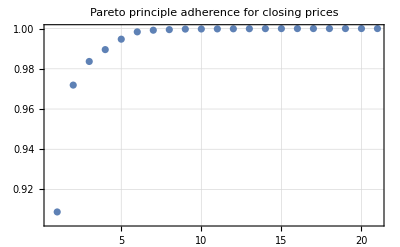

```mathematica
ListPlot[RakuInputExecute["pareto-principle-statistic(%prices)>>.value ==> encode-to-wl"],PlotTheme->"Detailed",PlotRange->All,PlotLabel->"Pareto principle adherence for closing prices"]
```

Here is the Pareto plot for trading volumes:

js-d3-list-plot(pareto-principle-statistic(%volumes)>>.value, 
                plot-label => 'Pareto principle adherence for trading volumes',
                width => 400, height => 300, 
                format => 'html', div-id => 'pareto-volumes'):grid-lines;

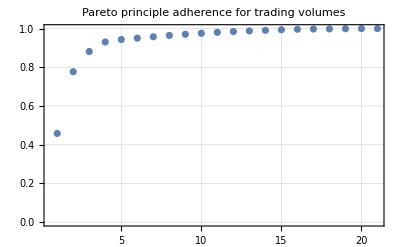

```mathematica
ListPlot[RakuInputExecute["pareto-principle-statistic(%volumes)>>.value ==> encode-to-wl"],PlotTheme->"Detailed",PlotRange->All,PlotLabel->"Pareto principle adherence for trading volumes"]
```

## References

### Articles

[AA1] Anton Antonov "Crypto-currencies data acquisition with visualization" , (2021), MathematicaForPrediction at WordPress .

[AA2] Anton Antonov "Cryptocurrencies data explorations" , (2021), MathematicaForPrediction at WordPress .

### Functions, packages

[AAf1] Anton Antonov, CryptocurrencyData Mathematica resource function, (2021). WolframCloud/antononcube .

[AAp1] Anton Antonov, Data::Cryptocurrencies Raku package , (2023). GitHub/antononcube .

[AAp2] Anton Antonov, JavaScript::D3 Raku package , (2022). GitHub/antononcube .

[AAp3] Anton Antonov, Text::CodeProcessing Raku package , (2021). GitHub/antononcube .

[AAp4] Anton Antonov, Markdown::Grammar , (2022). GitHub/antononcube .

## Setup

### Load RakuMode, and Raku encoder and decoder

```mathematica
Import["https://raw.githubusercontent.com/antononcube/ConversationalAgents/master/Packages/WL/RakuMode.m"];
Import["https://raw.githubusercontent.com/antononcube/ConversationalAgents/master/Packages/WL/RakuDecoder.m"];
Import["https://raw.githubusercontent.com/antononcube/ConversationalAgents/master/Packages/WL/RakuEncoder.m"];
SetOptions[RakuInputExecute,Epilog->FromRakuCode];
SetOptions[Dataset,MaxItems->{Automatic,40}];
```

### UML diagrams package

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/Misc/UMLDiagramGeneration.m"]
SetOptions[JavaPlantUML,"ExportDirectory"->"/tmp"];
```

### Raku mode

```mathematica
RakuMode[]
```

### Raku process

```mathematica
KillRakuProcess[]
StartRakuProcess["Raku"->$HomeDirectory<>"/.rakubrew/shims/raku"]
```

<|Process→ProcessObject[…],Socket→SocketObject[…]|>

use Data::Cryptocurrencies;
use Data::Reshapers;
use Data::Summarizers;
use Text::Plot;
use JavaScript::D3;

(Any)

### Load Raku packages

use Text::Plot;
use Stats;

use ML::AssociationRuleLearning;
use ML::Clustering;
use ML::StreamsBlendingRecommender;
use ML::ROCFunctions;
use ML::TriesWithFrequencies;
use Statistics::OutlierIdentifiers;

use Data::ExampleDatasets;
use Data::Generators;
use Data::Reshapers;
use Data::Summarizers;

use Mathematica::Serializer;
use UML::Translators;

use DSL::Shared::Utilities::ComprehensiveTranslation;

(Any)

### Shell

source ~/.zshrc

Success[…]